```mathematica
Clear["Global`*"];
cl=4250; ct=0.47 cl; cf=1500; d=0.0005; 
(*cl=3.5; ct=3; cf=1; d=1; *)
(*Ω=1/d/Sqrt[1/cf^2-1/ct^2] ArcTan[ρ0m Sqrt[(1-(ct/cl)^2)/((ct/cf)^2-1)]];*)
F1[k_,ω_,ρ0m_]:=((2 ω^2/cf^2-ω^2/ct^2-2 k^2)^2-4 √(ω^2/cf^2-ω^2/ct^2-k^2)√(ω^2/cf^2-ω^2/cl^2-k^2)(ω^2/cf^2-k^2)) Sin[k d/2]-
ρ0m  (ω/ct)^4 √(ω^2/cf^2-ω^2/cl^2-k^2)/k Cos[k d/2];
F1im[k_,ω_,ρ0m_]:=((2 ω^2/cf^2-ω^2/ct^2+2 k^2)^2-4 √(ω^2/cf^2-ω^2/ct^2+k^2)√(ω^2/cf^2-ω^2/cl^2+k^2)(ω^2/cf^2+k^2)) Sinh[k d/2]+
ρ0m  (ω/ct)^4 √(ω^2/cf^2-ω^2/cl^2+k^2)/k Cosh[k d/2];
F2[k_,ω_,ρ0m_]:=((2 ω^2/cf^2-ω^2/ct^2-2 k^2)^2-4 √(ω^2/cf^2-ω^2/ct^2-k^2)√(ω^2/cf^2-ω^2/cl^2-k^2)(ω^2/cf^2-k^2));
FF1[β_,ω_,ρ0m_]:=((2 β^2-ω^2/ct^2)^2-4 β^2 √(β^2-ω^2/ct^2)√(β^2-ω^2/cl^2))Sin[√(ω^2/cf^2-β^2) d/2]-
ρ0m  (ω/ct)^4 √(β^2-ω^2/cl^2)/√(ω^2/cf^2-β^2) Cos[√(ω^2/cf^2-β^2) d/2];
FF2[β_,ω_,ρ0m_]:=((2 β^2-ω^2/ct^2)^2-4 β^2 √(β^2-ω^2/ct^2)√(β^2-ω^2/cl^2))Sinh[√(β^2-ω^2/cf^2) d/2]+
ρ0m  (ω/ct)^4 √(β^2-ω^2/cl^2)/√(β^2-ω^2/cf^2) Cosh[√(β^2-ω^2/cf^2) d/2];
FF3[ξ_,ρ0m_]:=ArcCoth[(-(2-ξ^2)^2+4 √(1-ξ^2)√(1-(ct/cl)^2 ξ^2))/ρ0m/ξ^4/√(1-(ct/cl)^2 ξ^2)*√(1-(ct/cf)^2 ξ^2)]/√(1-(ct/cf)^2 ξ^2)2 ct;
```

```mathematica
mn={{0,0}};
For[i=1,i≤997,i++,
mn=Join[mn,{{FF3[cf/ct i/1000,0.12]/ct/(cf/ct i/1000),cf/ct i/1000}}]];
With[{ρ0m=0.12},
ins1=ListPlot[mn,Joined->True,PlotStyle->{Blue,Thick},BaseStyle->{FontSize->23},PlotRange->{{0,0.25},{0.,cf/ct}},FrameLabel->{"βd","ξ"},AspectRatio->0.5,Frame->True,FrameTicks->{{{0,0.2,0.4,0.6,{cf/ct,"c_f/c_t"}},None},{{0,0.1,0.2},None}},FrameStyle->Directive[Black]];
ins2=Plot[cf/ct,{x,0,0.25},PlotStyle->{Black,Thick},BaseStyle->{FontSize->23},PlotRange->{{0,0.25},{0.,cf/ct}},FrameLabel->{"βd","ξ"},AspectRatio->0.5,Frame->True,FrameTicks->{{{0,0.2,0.4,0.6,{cf/ct,"c_f/c_t"}},None},{{0,0.1,0.2},None}}];
p1=ContourPlot[{ξ==0.9999,ξ==0.936225,ξ==cf/ct,FF1[β,β ct ξ,ρ0m]==0},{β,0,40},{ξ,0.1,1},ContourStyle->{{Black,Thick},{Gray,Thick},{Black,Thick},{Red,Thick}},BaseStyle->{FontSize->23},PlotPoints->50,PlotRange->{{0,40},{0.2,1}},FrameLabel->{"βd","ξ"},AspectRatio->0.7,FrameStyle->Directive[Black],Epilog->{Inset[ins2,{20,0.45},Automatic,25],Inset[ins1,{20,0.45},Automatic,25]}];
p2=ListPlot[mn,Joined->True,PlotStyle->{Blue,Thick},BaseStyle->{FontSize->23},PlotRange->{{0,40},{0.,1}},FrameLabel->{"βd","ξ"},AspectRatio->0.25];
Show[{p1,p2}]]
```

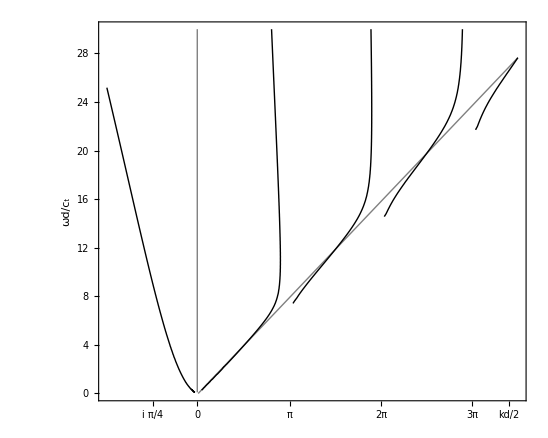

```mathematica
With[{ρ0m=0.01},
pl1ins=ContourPlot[{ω==2Pi k/√(ct^2/cf^2-(0.936225)^-2),F1[2Pi k/d,ω ct/d,ρ0m]==0},{k,0,4.2},{ω,0,40},ContourStyle->{{Black,Thin},{Black,Thick}},PlotRange->{{0,4.2},{0,40}},FrameLabel->{None,"ωd/c_t"},FrameTicks->{{{0,"0"},{1,"π"},{2,"2π"},{3,"3π"},{4.2,"kd/2"}},Automatic},BaseStyle->{FontSize->19},PlotPoints->50];]
With[{ρ0m=0.12},
pl1=ContourPlot[{ω==2Pi k/√(ct^2/cf^2-(0.936225)^-2),F1[2Pi k/d,ω ct/d,ρ0m]==0},{k,0,3.5},{ω,0,30},ContourStyle->{{Gray,Thin},{Black,Thick}},PlotRange->{{-1,3.5},{0,30}},FrameLabel->{None,"ωd/c_t"},FrameTicks->{{{-0.5,i"π/4"},{-0.01,"0"},{1,"π"},{2,"2π"},{3,"3π"},{3.4,"kd/2"}},Automatic},BaseStyle->{FontSize->25},PlotPoints->50,Epilog->Inset[pl1ins,{2.5,7},Automatic,1.65],AspectRatio->0.8];
pl2=ContourPlot[{F1im[-2Pi k/d/2,ω ct/d,ρ0m]==0,k==-0.01},{k,-1,0},{ω,0.1,30},ContourStyle->{{Black,Thick},{Gray,Thin}},PlotRange->{{-1,3.5},{0,30}},FrameLabel->{None,"ωd/c_t"},(*FrameTicks->{{{0,"0"},{0.25,"iπ/4"},{0.5,"kd/2"}},Automatic},*)BaseStyle->{FontSize->25},PlotPoints->50,AspectRatio->0.8];
Show[pl1,pl2]]
```

```mathematica
Style["i",Italic]
```

i

```mathematica
FF1[q_,Ω_,ρ0m_]:=((2 q^2-Ω^2)^2-4 q^2 √(q^2-Ω^2)√(q^2-Ω^2 ct^2/cl^2))Sin[√(Ω^2 ct^2/cf^2-q^2)/2]-
ρ0m Ω^4 √(q^2-Ω^2 ct^2/cl^2)/√(-Ω^2 ct^2/cf^2+q^2) Cos[√(Ω^2 ct^2/cf^2-q^2)/2];
With[{Ω=0.15},FindRoot[FF1[Ω/ξ,Ω,0.12]==0,{ξ,2-1I}]]
```

{ξ→1.22614-0.0899793 ⅈ}

```mathematica
(*ξ0=cl/ct;*)
r0m=0.12;
ansRe={};ansIm={};
OM=1/d/Sqrt[1/cf^2-1/ct^2] ArcTan[r0m Sqrt[(1-(ct/cl)^2)/((ct/cf)^2-1)]];
FF2[ks_,om_]:=Sin[(om/ct)d/2 Sqrt[(ct/cf)^2-(1/ks)^2]]((2(1/ks)^2-1)^2+4/ks^2 Sqrt[(1/ks)^2-1] Sqrt[(1/ks)^2-(ct/cl)^2])-r0m Sqrt[((1/ks)^2-(ct/cl)^2)]/Sqrt[((ct/cf)^2-(1/ks)^2)] Cos[(om/ct)d/2 Sqrt[(ct/cf)^2-(1/ks)^2]];
Do[
If[vi<50,ksi31=Y/.FindRoot[FF2[Y,vi OM]==0,{Y,1.3}];
If[Re[ksi31]<0,ksi31=-ksi31];If[Im[ksi31]<0,ksi31=Conjugate[ksi31]]];
ansRe=Join[ansRe,{{vi OM d/ct,Re[ksi31]}}];
ansIm=Join[ansIm,{{vi OM d/ct,Im[ksi31]}}];
(*ξ0=x;*)
,{vi,0.01,50.01,0.1}]
```

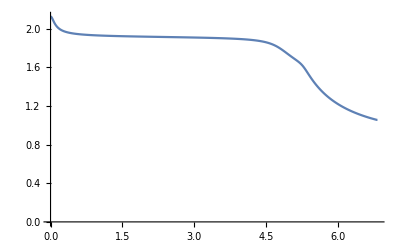

```mathematica
ListPlot[ansRe,PlotRange->All,Joined->True]
```

```mathematica
Export["C:\\Users\\Andri_000\\Documents\\Im.csv",ansIm,"CSV"]
```

C:\Users\Andri_000\Documents\Im.csv

```mathematica
cl/ct
```

2.12766